```mathematica
NotebookSave[];
```

### Init

```mathematica
tplus=(mB+mK)^2;
tminus=(mB-mK)^2;
tzero=tplus(1-Sqrt[1-tminus/tplus]);
```

```mathematica
z[t_]=(Sqrt[tplus-t]-Sqrt[tplus-tzero])/(Sqrt[tplus-t]+Sqrt[tplus-tzero]);
```

```mathematica
F[q.b2_,x_]=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](z[q.b2]-z[0])^k,{k,0,2}]//Simplify;
```

```mathematica
formFactors={fplus[q.b2_]:> F[q.b2,fplus], fzero[q.b2_]:> F[q.b2,fzero]};
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 };
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,MB:>4.18,mb:>4.18,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MT:>173,mt:>173,MS:>0.095,ms:>0.095,mB:>5.279,mK:>0.4937,mπ:>0.14,mD:>1.86,v:>246,me:>0.000511,mμ:>0.106,mτ:>1.777,MD:>0.0047,md:>0.0047,Γh:>0.013,mBs:>5.367,fBs:>0.227,mBd:>5.280,fBd:>0.188};
ckms={CKM[3,3]:>0.999,Vtb:>0.999,CKM[3,2]:>0.0404,Vts:>0.0404,CKM[2,3]:>0.0412,Vcb:>0.0412,CKM[2,2]:>0.973,Vcs:>0.973, Vtd:> 8.1/1000};
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181,Subscript[X,t]:>1.469,sw.b2:>0.231};
eulergamma={Subscript[γ,E]:>0.5772};
```

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2)
Γϕf[mϕ_,α_]:=Sum[HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2)),{mf,{me,mμ,mτ,MU,MD,MS,MC,MB,MT}}]/(8 π mϕ^2)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2)
Γϕg[mϕ_,α_]:=9/8 alphas^2/alphaem^2*Γϕγ[mϕ,α]
(*possibly add to scalars at high enough masses*)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α]+ΓϕZ[mϕ,α]+ΓϕW[mϕ,α]+Γϕγ[mϕ,α]+Γϕg[mϕ,α])/.masses/.couplings
```

### B -> K μμ width

```mathematica
(* The interesting part about the B->Kμμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/Γϕ[mϕ,mχ,ξ,α]
```

```mathematica
ΓBtoKϕ[mϕ_,α_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fzero[mϕ^2]^2 (mB-mK)^2 (mB+mK)^2 (MB+MS)^2 Sqrt[(mB+mK-mϕ) (mB-mK+mϕ) (mB^2-(mK+mϕ)^2)] (2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2 (MW^2-MT^2)^6)
```

```mathematica
Γϕtoμμ[mϕ_,α_]:=HeavisideTheta[mϕ-2 mμ] ((mμ/v)^2 Sin[α]^2 (mϕ^2-4 mμ^2)^(3/2))/(8 π mϕ^2)
```

```mathematica
(* Plot ΓBtoKμμ for the biggest possible angle (~.080.005) below where it can decay into DM and from that calculate the lifetime and decay length *)
```

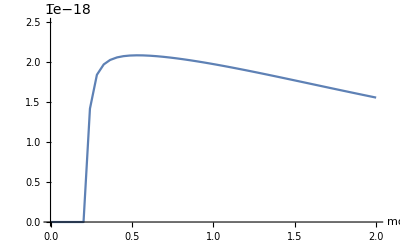

```mathematica
Plot[ΓBtoKμμ[mϕ,1,1,0.005]/.{qH.b2:>mϕ^2}/.formFactors/.values/.masses/.couplings/.ckms,{mϕ,0,2},AxesLabel->{mϕ,Γ},PlotRange->{0,2.5*10^-18}]
```

Power::infy: Infinite expression 1/0 encountered.

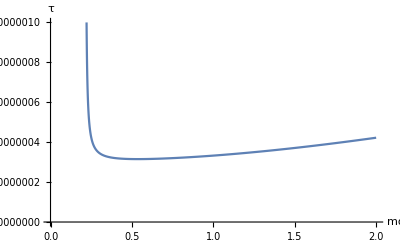

```mathematica
Plot[6.582*10^-25/ΓBtoKμμ[mϕ,1,1,0.005]/.{qH.b2:>mϕ^2}/.formFactors/.values/.masses/.couplings/.ckms,{mϕ,0,2},AxesLabel->{mϕ,τ},PlotRange->{0,10^-6}]
```

### Boost defs

```mathematica
boostϕ[boostB_,mϕ_]:=(boostB mB)/(2mϕ)
```

```mathematica
BelleIIboostB=0.284
```

0.284

```mathematica
LHCbboostB=15.2
```

15.2

```mathematica
BelleIImaxlength=0.14
```

0.14

```mathematica
LHCbmaxlength=0.6 (*m*)
```

0.6

```mathematica
boostedDecayLength[boostB_,mϕ_,mχ_,ξ_,α_]:=boostϕ[boostB,mϕ]*hbarc/Γϕ[mϕ,mχ,ξ,α]/.formFactors/.values/.masses/.couplings/.ckms/.{hbarc:>197/10^18 (* GeV m *)}
```

```mathematica
(* units: [bdl]=m,[hbarc]=GeV m, [Γ]=GeV, check *)
```

```mathematica
boostedDecayLength[15,1,1,1,x]==0.6//Solve
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.000153285},{x→0.000153285}}

### Plots

#### in mϕ

```mathematica
bdlPlot[α_]:=LogLogPlot[{boostedDecayLength[BelleIIboostB,mϕ,1000,0,α],BelleIImaxlength,boostedDecayLength[LHCbboostB,mϕ,1000,0,α],LHCbmaxlength},{mϕ,0.25,5},AxesLabel->{"mϕ [GeV]","boosted decay length [m]"},PlotLegends->{"bdl@BelleII","detectorsize@BelleII","bdl@LHCb","detectorsize@LHCb"},PlotLabel->StringForm["α=``",α],PlotRange->{0.001,100}]
```

InterpolatingFunction::dmval: Input value {0.250015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

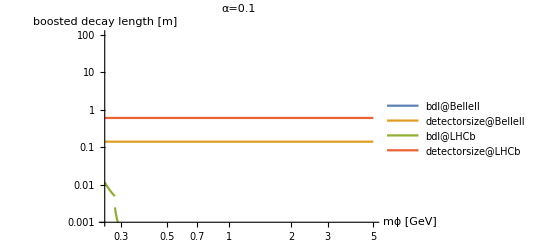

```mathematica
bdlPlot[0.1]
```

InterpolatingFunction::dmval: Input value {0.250015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

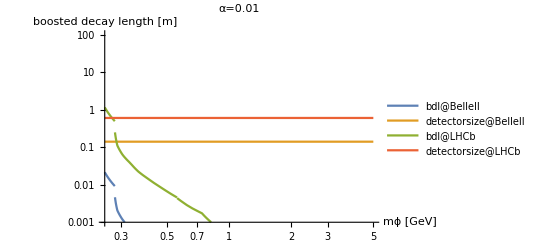

```mathematica
bdlPlot[0.01]
```

InterpolatingFunction::dmval: Input value {0.250015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

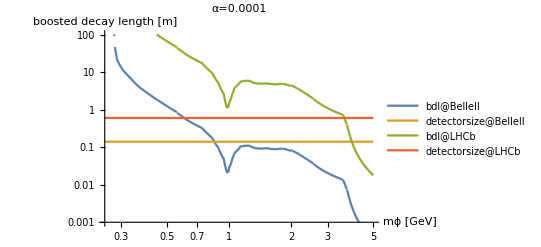

```mathematica
bdlPlot[0.0001]
```

#### in α

```mathematica
bdlPlotinαB2[mϕ_]:=LogLinearPlot[{boostedDecayLength[BelleIIboostB,mϕ,1000,0,α],BelleIImaxlength},{α,10^-5,π/4},AxesLabel->{"α","boosted decay length [m]"},PlotLegends->{"bdl","dl"},PlotLabel->StringForm["Belle II, mϕ=`` GeV",mϕ]]
bdlPlotinαLb[mϕ_]:=LogLinearPlot[{boostedDecayLength[LHCbboostB,mϕ,1000,0,α],LHCbmaxlength},{α,10^-5,π/4},AxesLabel->{"α","boosted decay length [m]"},PlotLegends->{"bdl","dl"},PlotLabel->StringForm["LHCb, mϕ=`` GeV",mϕ],PlotRange->{0,1.5}]
```

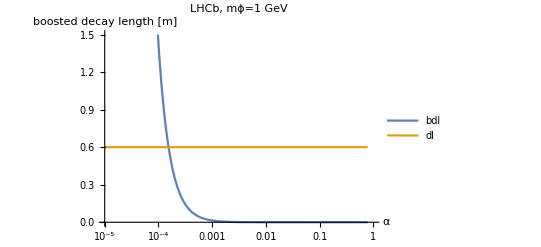

```mathematica
bdlPlotinαLb[1]
```

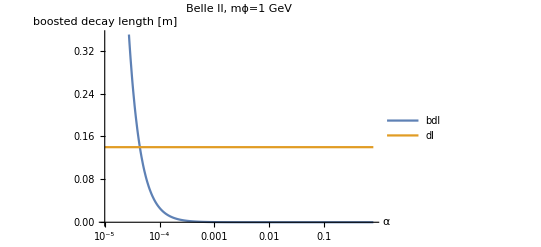

```mathematica
bdlPlotinαB2[1]
```

#### in mϕ-α (Contour)

InterpolatingFunction::dmval: Input value {0.000357143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

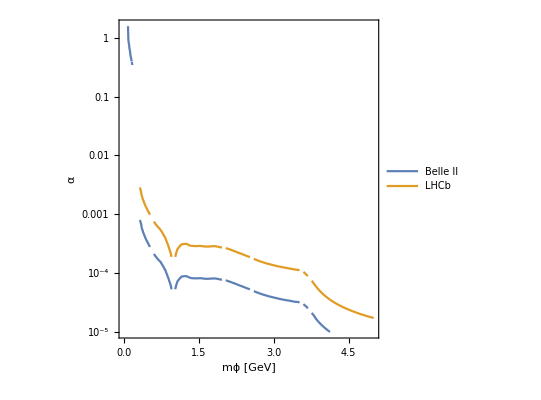

```mathematica
ContourPlot[{boostedDecayLength[BelleIIboostB,mϕ,1000,0,α]==BelleIImaxlength,boostedDecayLength[LHCbboostB,mϕ,1000,0,α]==LHCbmaxlength},{mϕ,0,5},{α,10^-5,π/2},FrameLabel->{"mϕ [GeV]","α"},PlotLegends->{"Belle II","LHCb"},ScalingFunctions->{"Linear","Log"}]
```

### Fraction of invisible muon decays

```mathematica
invisiblefraction[dl_,bdl_]:=Exp[-dl/bdl]
```

```mathematica
ifLHCb[mϕ_,mχ_,ξ_,α_]:=invisiblefraction[LHCbmaxlength,boostedDecayLength[LHCbboostB,mϕ,mχ,ξ,α]]
```

```mathematica
ifBelleII[mϕ_,mχ_,ξ_,α_]:=invisiblefraction[BelleIImaxlength,boostedDecayLength[BelleIIboostB,mϕ,mχ,ξ,α]]
```

```mathematica
ifplot[mϕ_]:=LogLinearPlot[{ifLHCb[mϕ,100,0,α],ifBelleII[mϕ,100,0,α]},{α,10^-6,0.01},AxesLabel->{"α","invisible fraction"},PlotLabel->StringForm["mϕ=``GeV",mϕ],PlotStyle->{Plain, Dotted},PlotLegends->{LHCb,BelleII},PlotRange->{0,1}]
```

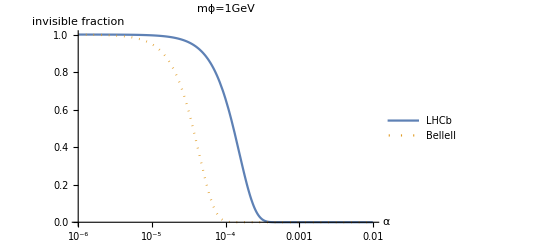

```mathematica
ifplot[1]
```

InterpolatingFunction::dmval: Input value {2.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

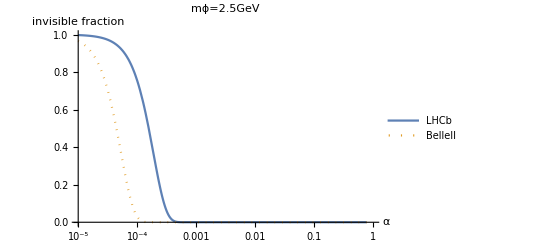

```mathematica
ifplot[2.5]
```

### Stuff copied from hadronicRates_tidy.nb

```mathematica
m23.b2plus[q.b2_,mχ_]=m23.b2/.(Solve[q.b2==4 (mχ^2+p1.b2)&&q.b2==mB^2+mK^2-2 Sqrt[mB^2+p3.b2] Sqrt[mK^2+p3.b2]+2 p3.b2&&m23.b2==mK^2+mχ^2+2 Sqrt[mχ^2+p1.b2] Sqrt[mK^2+p3.b2]+2 Sqrt[p1.b2] Sqrt[p3.b2],{p1.b2,p3.b2,m23.b2}]//Simplify//#//.{Sqrt[q.b2] Sqrt[a_/q.b2]:>Sqrt[a],Sqrt[a_^2]:>-a}&)[[1]]
m23.b2minus[q.b2_,mχ_]=m23.b2/.(Solve[q.b2==4 (mχ^2+p1.b2)&&q.b2==mB^2+mK^2-2 Sqrt[mB^2+p3.b2] Sqrt[mK^2+p3.b2]+2 p3.b2&&m23.b2==mK^2+mχ^2+2 Sqrt[mχ^2+p1.b2] Sqrt[mK^2+p3.b2]-2 Sqrt[p1.b2] Sqrt[p3.b2],{p1.b2,p3.b2,m23.b2}]//Simplify//#//.{Sqrt[q.b2] Sqrt[a_/q.b2]:>Sqrt[a],Sqrt[a_^2]:>-a}&)[[1]]
```

1/2 (mB^2+mK^2+2 mχ^2-q.b2+√(-4 mχ^2+q.b2) √((mB^4+(mK^2-q.b2)^2-2 mB^2 (mK^2+q.b2))/(q.b2)))

1/2 (mB^2+mK^2+2 mχ^2-q.b2-√(-4 mχ^2+q.b2) √((mB^4+(mK^2-q.b2)^2-2 mB^2 (mK^2+q.b2))/(q.b2)))

```mathematica
dΓdq.b2hm[qH.b2_,mχ_,mϕ_,ξ_,α_]:=(((EL^6*(mB-mK)^2*(mB+mK)^2*(MB+MS)^2*MT^4*(-4*mχ^2+qH.b2)^(3/2)*Sqrt[(mB^4+(mK^2-qH.b2)^2-2*mB^2*(mK^2+qH.b2))/qH.b2]*Vtb^2*Vts^2*fzero[qH.b2]^2*((MT^2-MW^2)^2*(36*MT^8*(mϕ^4+Γ^2)-12*MT^6*(mϕ^4*qH.b2+12*MW^2*(mϕ^4+Γ^2))+MT^4*(60*MW^2*mϕ^4*qH.b2+mϕ^4*qH.b2^2+216*MW^4*(mϕ^4+Γ^2))-6*MT^2*(14*MW^4*mϕ^4*qH.b2+MW^2*mϕ^4*qH.b2^2+24*MW^6*(mϕ^4+Γ^2))+9*(4*MW^6*mϕ^4*qH.b2+MW^4*mϕ^4*qH.b2^2+4*MW^8*(mϕ^4+Γ^2))+MH^4*(36*MT^8-12*MT^6*(12*MW^2+qH.b2)+9*MW^4*(4*MW^4+4*MW^2*qH.b2+qH.b2^2+Γ^2)-6*MT^2*MW^2*(24*MW^4+14*MW^2*qH.b2+qH.b2^2+Γ^2)+MT^4*(216*MW^4+60*MW^2*qH.b2+qH.b2^2+Γ^2))-2*MH^2*(36*MT^8*mϕ^2-6*MT^6*(24*MW^2*mϕ^2+2*mϕ^2*qH.b2-Γ^2)+9*(4*MW^8*mϕ^2+MW^4*mϕ^2*qH.b2^2+MW^6*2*(2*mϕ^2*qH.b2-Γ^2))+MT^4*(216*MW^4*mϕ^2+mϕ^2*qH.b2^2+30*MW^2*(2*mϕ^2*qH.b2-Γ^2))-6*MT^2*(24*MW^6*mϕ^2+MW^2*mϕ^2*qH.b2^2+7*MW^4*(2*mϕ^2*qH.b2-Γ^2))))+4*MT^2*(MT^4-3*MT^2*MW^2+2*MW^4)*(mϕ^4*qH.b2*(6*MT^4+3*MW^2*(2*MW^2+qH.b2)-MT^2*(12*MW^2+qH.b2))+MH^4*(6*MT^4*qH.b2+3*MW^2*(2*MW^2*qH.b2+qH.b2^2+Γ^2)-MT^2*(12*MW^2*qH.b2+qH.b2^2+Γ^2))-2*MH^2*(3*MW^2*mϕ^2*qH.b2^2+MT^4*3*(2*mϕ^2*qH.b2-Γ^2)+MW^4*3*(2*mϕ^2*qH.b2-Γ^2)-MT^2*(mϕ^2*qH.b2^2+6*MW^2*(2*mϕ^2*qH.b2-Γ^2))))*Log[MT^2/MW^2]+4*MT^4*(MT^2-2*MW^2)^2*(-2*MH^2*mϕ^2*qH.b2^2+mϕ^4*qH.b2^2+MH^4*(qH.b2^2+Γ^2))*Log[MT^2/MW^2]^2))/(33554432*mB^3*(MB-MS)^2*(MT-MW)^6*MW^6*(MT+MW)^6*Pi^7*(MH^2-qH.b2)^2*SW^6*(mϕ^4-2*mϕ^2*qH.b2+qH.b2^2+Γ^2)))//#/.{Γ:>Γϕ[mϕ,mχ,ξ,α]}&)
```

```mathematica
Γhm[mχ_,mϕ_?NumericQ,ξ_,α_]:=(*Sin[α]^2 Cos[α]^2 ξ^2*)NIntegrate[dΓdq.b2hm[qH.b2,mχ,mϕ,ξ,α]/.formFactors/.values/.masses/.ckms/.couplings/.MH:>125,{qH.b2,(2 mχ)^2,(mB-mK)^2/.masses}]
```

```mathematica
dΓdq.b2SMνν[q.b2_]=1/((2 π)^3 32 mB^3)*2*Subscript[α,em]^2/π^2*3 GF^2 Vtb^2 Vts^2 Subscript[X,t]^2/sw.b2^2 (Abs[fplus[q.b2]])^2 Integrate[((mB^2-m23.b2) (m23.b2+q.b2-mK^2)-mB^2 q.b2),{m23.b2,m23.b2minus[q.b2,0],m23.b2plus[q.b2,0]}]//Simplify
```

(GF^2 (q.b2)^(3/2) ((mB^4+(mK^2-q.b2)^2-2 mB^2 (mK^2+q.b2))/(q.b2))^(3/2) Vtb^2 Vts^2 Abs[fplus[q.b2]]^2 X_t^2 α_em^2)/(256 mB^3 π^5 (sw.b2)^2)

```mathematica
ΓSMνν=NIntegrate[dΓdq.b2SMνν[q.b2]/.formFactors/.values/.masses/.ckms/.couplings/.MH:>125,{q.b2,0,(mB-mK)^2/.masses}]
```

1.61138×10^-18

```mathematica
hmFactor[ξ_,α_]:=Sin[α]^2 Cos[α]^2 ξ^2
```

```mathematica
Γtotal=6.582*10^-25/(1.638*10^-12);
BRSMνν=ΓSMνν/(Γtotal);
BRhm[mχ_,mϕ_,ξ_,α_]:=Γhm[mχ,mϕ,ξ,α] hmFactor[ξ,α]/Γtotal
```

```mathematica
RKhm[mχ_,mϕ_,ξ_,α_]:=(BRSMνν+BRhm[mχ,mϕ,ξ,α])/BRSMνν
```

```mathematica
BRexp=1.6*10^(-5);
```

```mathematica
RKexp=BRexp/BRSMνν;
```

```mathematica
Γhχ[mχ_,ξ_,α_]:=1/(8 π 125^2) HeavisideTheta[125-2 mχ] ξ^2 Sin[α]^2 (125^2-4 mχ^2)^(3/2)
ΓhSM=4/1000;
```

```mathematica
hmColour=ColorData[97,"ColorList"][[6]]
```

RGBColor[0.772079, 0.431554, 0.102387]

### Translation into new Rχ bounds

```mathematica
Rχhmfull[mχ_,mϕ_,ξ_,α_]:=(RKhm[mχ,mϕ,ξ,α]+ifBelleII[mϕ,α](ΓBtoKμμ[mϕ,mχ,ξ,α]/Γtotal)/BRSMνν)/.formFactors/.values/.masses/.ckms/.couplings/.MH:>125
```

```mathematica
Rinvμ[mϕ_,α_]:=((ifBelleII[mϕ,1000,0,α](ΓBtoKϕ[mϕ,α]*Γϕf[mϕ,α,mμ]/Γϕ[mϕ,1000,0,α]/Γtotal))/BRSMνν)/.formFactors/.values/.masses/.ckms/.couplings/.MH:>125 
(*if χ doesn't exist is the same as if it is too heavy or there's no coupling to it. *)
(* Rinvμ = Rχhmwoχ-1 *)
```

```mathematica
Rinvμ[1,5/10^5]
```

8.56731×10^-7+0. ⅈ

```mathematica
Rinvμplot[mϕ_]:=LogLogPlot[{Rinvμ[mϕ,α]},{α,10^-7,1},AxesLabel->{"α",Subscript[R, inv. μ]}]
```

InterpolatingFunction::dmval: Input value {0.222} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

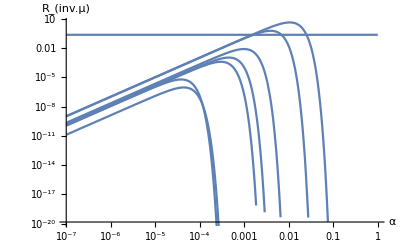

```mathematica
Show[Rinvμplot[2mμ+0.01/.masses],Rinvμplot[0.25],Rinvμplot[0.3],Rinvμplot[0.4],Rinvμplot[0.5],Rinvμplot[1],Rinvμplot[3],Rinvμplot[5],LogLogPlot[0.22,{α,10^-7,1}]]
```

```mathematica
RKPlothm[mχ_,ξ_,limit_,αlimit_]:=Show[RegionPlot[{Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2 ΓhSM))<1.17-0.10*2||Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2 ΓhSM))>1.17+0.10*2,False,Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2 ΓhSM))<1.10-0.11*2||Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2 ΓhSM))>1.10+0.11*2,1/(1+Cos[α]^2 ΓhSM/Γhχ[mχ,ξ,α])>0.22,1/(1+Cos[α]^2 ΓhSM/Γhχ[mχ,ξ,α])>0.26},{mϕ,0,limit},{α,0,αlimit},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ϕ\)]\) [GeV]","α"},PlotLabel->StringForm["\!\(\*SubscriptBox[\(m\), \(χ\)]\)=``GeV,  ξ=``",mχ,ξ],PlotLegends->{"Signal strength μ, 2σ (CMS)","Signal strength μ, 2σ,(ATLAS)","μ (PDG) 2σ","invisible Higgs decay (CMS)","invisible Higgs Decay (ATLAS)"}],ContourPlot[{RKhm[mχ,mϕ,ξ,α]==1.22,RKhm[mχ,mϕ,ξ,α]==1.6,RKhm[mχ,mϕ,ξ,α]==RKexp,Rχhmfull[mχ,mϕ,ξ,α]==1.22,Rχhmfull[mχ,mϕ,ξ,α]==1.6,Rχhmfull[mχ,mϕ,ξ,α]==RKexp},{mϕ,0,limit},{α,0,αlimit},ContourShading->"None",FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ϕ\)]\) [GeV]","α"},PlotLabel->StringForm["\!\(\*SubscriptBox[\(m\), \(χ\)]\)=``GeV,  ξ=``",mχ,ξ],PlotLegends->{"Belle II B->K+χχ/νν, 50 \!\(\*SuperscriptBox[\(ab\), \(-1\)]\) (2σ)","Belle II B->K+χχ/νν, 5 \!\(\*SuperscriptBox[\(ab\), \(-1\)]\) (2σ)","B→Kνν bound (90% CL)","Belle II B->K+inv., 50 \!\(\*SuperscriptBox[\(ab\), \(-1\)]\) (2σ)","Belle II B->K+inv., 5 \!\(\*SuperscriptBox[\(ab\), \(-1\)]\) (2σ)","B→Kνν bound (90% CL)"},ContourStyle->{Directive[Dotted,Gray],Directive[Dashed,Gray],Gray,Directive[Dotted,hmColour],Directive[Dashed,hmColour],hmColour},MaxRecursion->3]]
```

```mathematica
ContourPlot[{Rinvμ[mϕ,α]==0.22,Rinvμ[mϕ,α]==0.6,Rinvμ[mϕ,α]==(RKexp-1)},{mϕ,0.2,0.3},{α,10^(-5),0.01},ContourShading->"None",FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ϕ\)]\) [GeV]","α"},PlotLegends->{"Belle II B->K+inv., 50 \!\(\*SuperscriptBox[\(ab\), \(-1\)]\) (2σ)","Belle II B->K+inv., 5 \!\(\*SuperscriptBox[\(ab\), \(-1\)]\) (2σ)","B→Kνν bound (90% CL)"},ContourStyle->{Directive[Dotted,hmColour],Directive[Dashed,hmColour],hmColour},MaxRecursion->3,ScalingFunctions->{None,"Log"}]
```

InterpolatingFunction::dmval: Input value {0.200007} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.200007} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

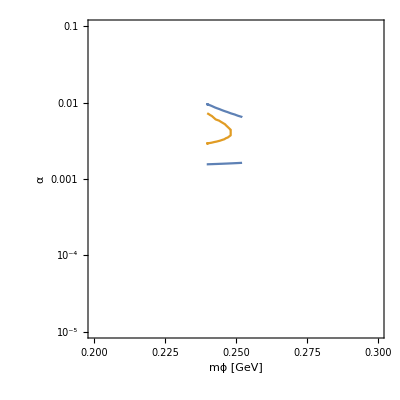

```mathematica
ContourPlot[{Rinvμ[mϕ,α]==0.22,Rinvμ[mϕ,α]==0.6,Rinvμ[mϕ,α]==(RKexp-1)},{mϕ,0.2,0.3},{α,10^(-5),0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"}]
```

InterpolatingFunction::dmval: Input value {0.0000714286} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

InterpolatingFunction::dmval: Input value {0.0000714286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

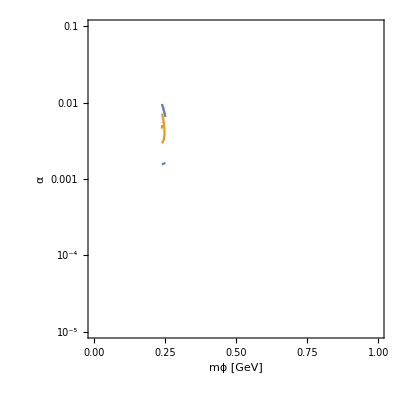

```mathematica
ContourPlot[{Rinvμ[mϕ,α]==0.22,Rinvμ[mϕ,α]==0.6,Rinvμ[mϕ,α]==(RKexp-1)},{mϕ,0,1},{α,10^(-5),0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"}]
```

```mathematica
RhmwoχPlot[1,10^-7,0.1]
```

InterpolatingFunction::dmval: Input value {0.0000714286} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

InterpolatingFunction::dmval: Input value {0.0000714286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
Rinvμ[mϕ,0.01]==0.22//NSolve
```

$Aborted

### Lifetime

```mathematica
hbardef={hbar:>6.58*10^(-13) (* GeV ps *)}
```

{hbar:>6.58/10^13}

```mathematica
τϕ[mϕ_,α_]:=hbar/Γϕ[mϕ,100,0,α]/.hbardef
```

```mathematica
Sin[x]^2τϕ[1,x]//Simplify
```

1.18932×10^-6

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

InterpolatingFunction::dmval: Input value {0.102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

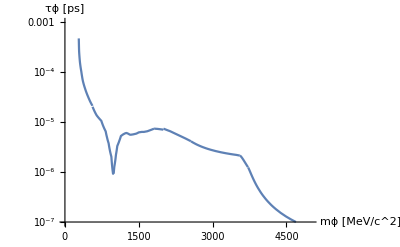

```mathematica
LogPlot[τϕ[y/1000,π/2],{y,0,5000},AxesLabel->{"mϕ [MeV/c^2]","τϕ [ps]"},PlotRange->{10^-7,10^-3}]
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

InterpolatingFunction::dmval: Input value {0.102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

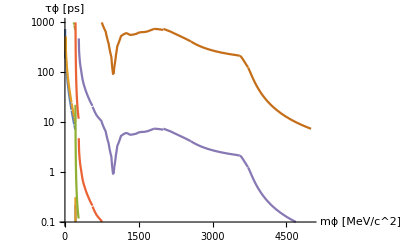

```mathematica
LogPlot[{τϕ[y/1000,π/2],τϕ[y/1000,1],τϕ[y/1000,0.1],τϕ[y/1000,0.01],τϕ[y/1000,0.001],τϕ[y/1000,0.0001]},{y,0,5000},AxesLabel->{"mϕ [MeV/c^2]","τϕ [ps]"},PlotRange->{10^-1,10^3}]
```

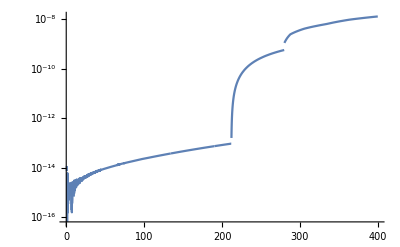

```mathematica
LogPlot[Γϕ[y/1000,1000,0,π/2],{y,0,400}]
```

```mathematica
τϕ[y/1000,π/2]
```

6.58×10^-13/(1/y^5 91.5868 ((y^4 (-362567.+(3 y^2)/1000000)^2)/1000000000000+229310730496 (-119716+y^2/1000000)^2 ArcTanh[y/(1000 √(-119716+y^2/1000000))]^4-0.465188 y^2 (-12921.9+y^2/1000000) (-362567.+(3 y^2)/1000000) ArcTanh[y/(1000 √(-25843.8+y^2/1000000))]^2+3.38125×10^9 (2.6716×10^9-0.4135 y^2+(17 y^4)/1000000000000) ArcTanh[y/(1000 √(-25843.8+y^2/1000000))]^4+957728 (-119716+y^2/1000000) ArcTanh[y/(1000 √(-119716+y^2/1000000))]^2 ((y^2 (-362567.+(3 y^2)/1000000))/1000000-232594. (-12921.9+y^2/1000000) ArcTanh[y/(1000 √(-25843.8+y^2/1000000))]^2))+1/y^2 0.51673 √(-33262.5+y^2/1000000) (5.00926×10^8-0.0198739 y^2+5.91361×10^-13 y^4) HeavisideTheta[-182.38+y/1000]+1/y^2 1.2223 √(-25843.8+y^2/1000000) (5.00926×10^8-0.0258438 y^2+y^4/1000000000000) HeavisideTheta[-160.76+y/1000]+(2.07618 (-12.6309+y^2/1000000)^(3/2) HeavisideTheta[-3.554+y/1000])/y^2+(34.4638 (-111.471+y^2/1000000)^(3/2) HeavisideTheta[-10.558+y/1000] HeavisideTheta[-2+y/1000])/y^2+(3.2317 (-13.8384+y^2/1000000)^(3/2) HeavisideTheta[-3.72+y/1000] HeavisideTheta[-2+y/1000])/y^2+(0.0178016 (-0.974959+y^2/1000000)^(3/2) HeavisideTheta[-2+y/1000] HeavisideTheta[-0.9874+y/1000])/y^2+5.1×10^-15 y^2 √(-0.0784+y^2/1000000) HeavisideTheta[2-y/1000] HeavisideTheta[-0.56+y/1000]+(0.00738757 (-0.044944+y^2/1000000)^(3/2) HeavisideTheta[-0.212+y/1000])/y^2+(1.71685×10^-7 (-1.04448×10^-6+y^2/1000000)^(3/2) HeavisideTheta[-0.001022+y/1000])/y^2+HeavisideTheta[2-y/1000] HeavisideTheta[-0.28+y/1000] InterpolatingFunction[…][y/1000]+HeavisideTheta[2-y/1000] HeavisideTheta[-0.9874+y/1000] InterpolatingFunction[…][y/1000]+1/(1936512000000000 π^3)y^3 Abs[1/y^4 14331920656000000000000 (y^2/119716000000+(-1+y^2/119716000000) (ArcSin[(√(y^2))/346000]^2 HeavisideTheta[1-y^2/119716000000]-1/4 HeavisideTheta[-1+y^2/119716000000] (-ⅈ π+Log[(1+√(1-119716000000/y^2))/(1-√(1-119716000000/y^2))])^2))+1/y^4 4.88456×10^15 (1.43083×10^-8 y^2+(-1+1.43083×10^-8 y^2) (ArcSin[0.000119617 √(y^2)]^2 HeavisideTheta[1-1.43083×10^-8 y^2]-1/4 HeavisideTheta[-1+1.43083×10^-8 y^2] (-ⅈ π+Log[(1+√(1-(6.98896×10^7)/y^2))/(1-√(1-(6.98896×10^7)/y^2))])^2))+1/y^4 4.29497×10^13 (1.52588×10^-7 y^2+(-1+1.52588×10^-7 y^2) (ArcSin[0.000390625 √(y^2)]^2 HeavisideTheta[1-1.52588×10^-7 y^2]-1/4 HeavisideTheta[-1+1.52588×10^-7 y^2] (-ⅈ π+Log[(1+√(1-(6.5536×10^6)/y^2))/(1-√(1-(6.5536×10^6)/y^2))])^2))+1/y^4 1.30321×10^9 (0.0000277008 y^2+(-1+0.0000277008 y^2) (ArcSin[0.00526316 √(y^2)]^2 HeavisideTheta[1-0.0000277008 y^2]-1/4 HeavisideTheta[-1+0.0000277008 y^2] (-ⅈ π+Log[(1+√(1-36100./y^2))/(1-√(1-36100./y^2))])^2))+1/y^4 7807.49 (0.0113173 y^2+(-1+0.0113173 y^2) (ArcSin[0.106383 √(y^2)]^2 HeavisideTheta[1-0.0113173 y^2]-1/4 HeavisideTheta[-1+0.0113173 y^2] (-ⅈ π+Log[(1+√(1-88.36/y^2))/(1-√(1-88.36/y^2))])^2))+1/y^4 374.81 (0.0516529 y^2+(-1+0.0516529 y^2) (ArcSin[0.227273 √(y^2)]^2 HeavisideTheta[1-0.0516529 y^2]-1/4 HeavisideTheta[-1+0.0516529 y^2] (-ⅈ π+Log[(1+√(1-19.36/y^2))/(1-√(1-19.36/y^2))])^2))]^2 HeavisideTheta[-2+y/1000] (InterpolatingFunction[…][y/1000])^2)

```mathematica
f[x]/Sin[α]^2==y//Solve[#,{α}]&
```

{{α→ConditionalExpression[-ArcSin[(√f[x])/(√y)]+2 π C[1],C[1]∈ℤ]},{α→ConditionalExpression[π-ArcSin[(√f[x])/(√y)]+2 π C[1],C[1]∈ℤ]},{α→ConditionalExpression[ArcSin[(√f[x])/(√y)]+2 π C[1],C[1]∈ℤ]},{α→ConditionalExpression[π+ArcSin[(√f[x])/(√y)]+2 π C[1],C[1]∈ℤ]}}

```mathematica
ArcSin[Sqrt[τϕ[3000/1000,π/2]]/Sqrt[10]]
```

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.00052326+0. ⅈ

InterpolatingFunction::dmval: Input value {0.000357143} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.357143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

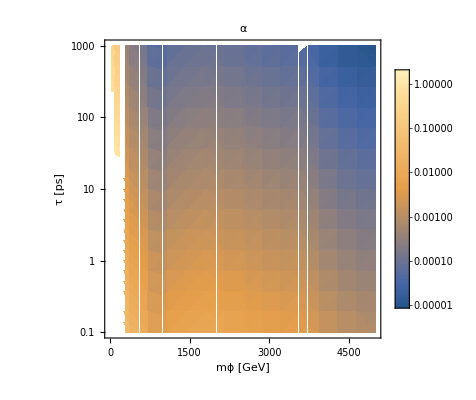

```mathematica
DensityPlot[ArcSin[Sqrt[τϕ[mϕ/1000,π/2]]/Sqrt[τ]],{mϕ,0,5000},{τ,10^-1,10^3},ScalingFunctions->{None,"Log","Log"},PlotLegends->Automatic,PlotLabel->"α",FrameLabel->{"mϕ [GeV]","τ [ps]"}]
```

### New ϕ-widths with mesons included

```mathematica
datapointsππ={{0.28001323,5.17024*10^(-10)},{0.27784854,1.0525554*10^(-9)},{0.2877911,1.8218304*10^(-9)},{0.30592537,3.3623317*10^(-9)},{0.33365947,5.277515*10^(-9)},{0.3639078,8.283586*10^(-9)},{0.41079497,1.2181233*10^(-8)},{0.47179008,1.7907567*10^(-8)},{0.5560635,2.7178222*10^(-8)},{0.6442094,4.2615103*10^(-8)},{0.73974603,5.5053757*10^(-8)},{0.8280175,9.213942*10^(-8)},{0.8877805,1.6462049*10^(-7)},{0.9437583,3.1379568*10^(-7)},{0.97783643,7.033213*10^(-7)},{1.002676,3.6842826*10^(-7)},{1.036807,1.5896644*10^(-7)},{1.0629779,7.317836*10^(-8)},{1.108985,3.958082*10^(-8)},{1.1371115,2.0074902*10^(-8)},{1.1865596,1.27616815*10^(-8)},{1.2277195,9.23311*10^(-9)},{1.2817607,8.933028*10^(-9)},{1.3385478,1.08358424*10^(-8)},{1.3852515,9.2141486*10^(-9)},{1.47,4.38*10^(-9)},{1.5,2.5269602*10^(-9)},{1.5614661,4.1001567*10^(-9)},{1.6033295,6.6537464*10^(-9)},{1.6742321,7.566051*10^(-9)},{1.7473112,5.4732547*10^(-9)},{1.8077103,3.5941348*10^(-9)},{1.88713,3.25975*10^(-9)},{1.9999999,3.7056085*10^(-9)}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK={{0.992899,1.39798*10^(-7)},{1.07269,1.07816*10^(-7)},{1.13916,8.87269*10^(-8)},{1.25236,8.04012*10^(-8)},{1.31897,8.56912*10^(-8)},{1.45009,8.02007*10^(-8)},{1.58049,7.26857*10^(-8)}{1.69277,5.42831*10^(-8)},{1.81310,4.18707*10^(-8)},{1.99304,3.44371*10^(-8)}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.250016} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.265991} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.282986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

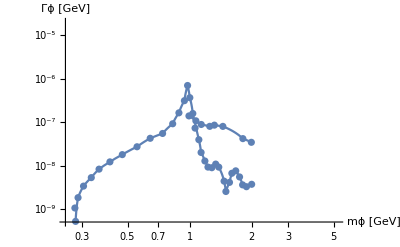

```mathematica
Show[LogLogPlot[{ΓϕKK[mϕ]*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ]},{mϕ,0.25,5.2},PlotRange->{{0.25,5.2},{5*10^(-10),2*10^(-5)}},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsKK,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],LogLogPlot[Γϕππ[mϕ]*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ],{mϕ,0.25,5.2},PlotRange->{5*10^(-10),2*10^(-5)},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsππ,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}]]
```

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
```

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
newWidthsPlot[α_]:=LogLogPlot[{Γϕ[mϕ,1000,0,α],Γϕf[mϕ,α,mμ]/.masses/.couplings,Γϕf[mϕ,α,mτ]/.masses/.couplings,Γϕπ[mϕ,α]/.masses/.couplings,ΓϕK[mϕ,α]/.masses/.couplings,Γϕmoreπs[mϕ,α]/.masses/.couplings,Γϕg[mϕ,α]/.{alphas:>AlphaS[mϕ]}/.masses/.couplings,Γϕs[mϕ,α]/.masses/.couplings,Γϕc[mϕ,α]/.masses/.couplings,Γϕb[mϕ,α]/.masses/.couplings,Γϕγ[mϕ,α]/.masses/.couplings,ΓϕW[mϕ,α]/.masses/.couplings,ΓϕZ[mϕ,α]/.masses/.couplings,Γϕf[mϕ,α,me]/.masses/.couplings},{mϕ,0.25,5.2},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"},PlotRange->{{0.25,5.2},{5*10^(-10),2*10^(-5)}},PlotLabels->{total,μ μ̄,τ τ̄,ππ,KK,"4π,ηη,ρρ,…",gg,s s̄,c c̄,b b̄,γγ,WW,ZZ,e ē},PlotStyle->{Directive[Dotted,Black],,,,,,,,,,,,,}]
```

```mathematica
newWidthsPlot[π/2]
```

InterpolatingFunction::dmval: Input value {0.250016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 11 in {934,83,113,657,236,76,141,54,108,25}.

Part::take: Cannot take positions 1 through 12 in {934,83,113,657,236,76,141,54,108,25}.

Part::take: Cannot take positions 1 through 13 in {934,83,113,657,236,76,141,54,108,25}.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

InterpolatingFunction::dmval: Input value {0.102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

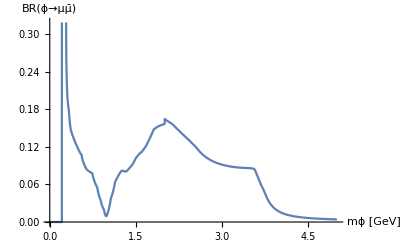

```mathematica
Plot[Γϕf[mϕ,π/2,mμ]/Γϕ[mϕ,1000,0,π/2]/.masses/.couplings,{mϕ,0,5},AxesLabel->{"mϕ [GeV]","BR(ϕ→μμ̄)"}]
```

### WIP

```mathematica
τϕ[mϕ_,α_,mχ_,ξ_]:=hbar/Γϕ[mϕ,mχ,ξ,α]/.hbardef
```

```mathematica
BRBtoKμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKμμ[mϕ,mχ,ξ,α]/Γtotal
```

```mathematica
fornoDM[mϕ_,α_]:={τϕ[mϕ,α],BRBtoKμμ[mϕ,100,0,α]/.{qH.b2:>mϕ^2}/.formFactors/.values/.masses/.couplings/.ckms}//Re//Simplify
```

```mathematica
fornoDM[1.25,0.00022]
```

{116.198,1.51288×10^-9}

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

InterpolatingFunction::dmval: Input value {0.102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

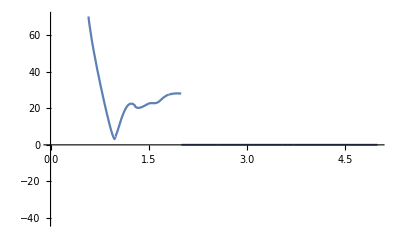

```mathematica
Plot[τϕ[m,0.0005,1,1],{m,0,5}]
```

```mathematica
whiteregions[m_]:=HeavisideTheta[m-0.25]HeavisideTheta[-m+0.4]+HeavisideTheta[m-0.5]HeavisideTheta[-m+2.9]+HeavisideTheta[m-3.2]HeavisideTheta[-m+3.6]+HeavisideTheta[m-3.9]HeavisideTheta[-m+4.7]
```

```mathematica
noDMdata={{0.3,6},{0.75,2.2},{1,3},{1.25,2.3},{1.5,1.7},{2,2.3},{2.75,1.7},{3.5,1},{4,1.5},{4.5,4}}
```

{{0.3,6},{0.75,2.2},{1,3},{1.25,2.3},{1.5,1.7},{2,2.3},{2.75,1.7},{3.5,1},{4,1.5},{4.5,4}}

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

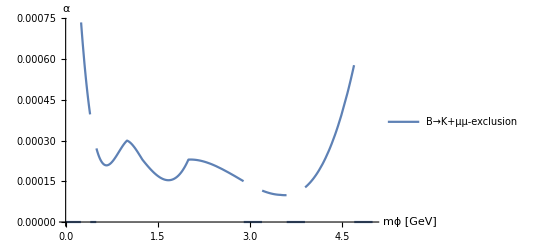

```mathematica
Plot[10^{-4}Interpolation[noDMdata][m]*whiteregions[m],{m,0,5},AxesLabel->{"mϕ [GeV]","α"},PlotLegends->{"B→K+μμ-exclusion"}]
```

```mathematica
RKPlothmWMuons[mχ_,ξ_,limit_,αlimit_]:=Show[RegionPlot[{Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2ΓhSM))<1.17-0.10*2||Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2ΓhSM))>1.17+0.10*2,Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2ΓhSM))<1.11-0.08*2||Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2ΓhSM))>1.11+0.09*2(*,Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2ΓhSM))<1.10-0.11*2||Cos[α]^2/(1+(Γhχ[mχ,ξ,α])/(Cos[α]^2ΓhSM))>1.10+0.11*2*)},{mϕ,0,limit},{α,0,αlimit},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ϕ\)]\) [GeV]","α"},PlotLabel->StringForm["\!\(\*SubscriptBox[\(m\), \(χ\)]\)=``GeV,  ξ=``",mχ,ξ],PlotLegends->{ "Signal strength μ, 2σ (CMS)","Signal strength μ, 2σ (ATLAS)"(*,"μ (PDG) 2σ"*)}],RegionPlot[{1/(1+Cos[α]^2 ΓhSM/Γhχ[mχ,ξ,α])>0.22,1/(1+Cos[α]^2 ΓhSM/Γhχ[mχ,ξ,α])>0.26},{mϕ,0,limit},{α,0,αlimit},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ϕ\)]\) [GeV]","α"},PlotLabel->StringForm["\!\(\*SubscriptBox[\(m\), \(χ\)]\)=``GeV,  ξ=``",mχ,ξ],PlotLegends->{ "invisible Higgs decay (CMS)","invisible Higgs Decay (ATLAS)"},BoundaryStyle->{Dashed, Dashed}],ContourPlot[{RKhm[mχ,mϕ,ξ,α]==1.22,RKhm[mχ,mϕ,ξ,α]==1.6,RKhm[mχ,mϕ,ξ,α]==RKexp},{mϕ,0,limit},{α,0,αlimit},ContourShading->"None",FrameLabel->{"m_ϕ [GeV]","α"},PlotLabel->StringForm["m_χ=``GeV,  ξ=``",mχ,ξ],PlotLegends->{"Belle II B->Kχχ, 50 ab^-1 (2σ)","Belle II B->Kχχ, 5 ab^-1 (2σ)","B→Kνν bound (90% CL)"},ContourStyle->{Directive[Dotted,hmColour],Directive[Dashed,hmColour],hmColour}, MaxRecursion->3],ContourPlot[{α==10^{-4}Interpolation[noDMdata][mϕ]*whiteregions[mϕ]*HeavisideTheta[-mϕ+2mχ]},{mϕ,0,limit},{α,0,αlimit},ContourShading->"None",FrameLabel->{"m_ϕ [GeV]","α"},PlotLabel->StringForm["m_χ=``GeV,  ξ=``",mχ,ξ],PlotLegends->{"LHCb invisible B→Kμμ"},ContourStyle->{Black}, MaxRecursion->3]]
```